```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12,Magnification->1.6};
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/AcoreNteraction/source_mathematica

```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=z SphericalBesselY[l,z];
```

```mathematica
(*alpha[r_,k_,l_,h_]:=(1+h (D[FunctionExpand[RiccatiBesselN[k x,l]],x]/.x->r)/(FunctionExpand[RiccatiBesselN[k r,l]]))
beta[r_,k_,l_,h_]:=h FunctionExpand[RiccatiBesselJ[k r,l]](((D[FunctionExpand[RiccatiBesselJ[k x,l]],x])/.x->r)/(FunctionExpand[RiccatiBesselJ[k r,l]])-((D[FunctionExpand[RiccatiBesselN[k x,l]],x])/.x->r)/(FunctionExpand[RiccatiBesselN[k r,l]]))*)
alpha[ra_,ka_,la_,ha_]:=RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]

beta[rb_,kb_,lb_,hb_]:=RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])
```

LEC=(Λ,a_(3-1)^(S-wave) [fm],C_(2-body) [MeV],C_(3-body) [MeV])
the triton-proton S-wave scattering length is used to calibrate the core parameter and
was obtained by R. Lazauskas.

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
a0a1NUCLmartinrimas=Import[NotebookDirectory[]<>"../data/a0-a1_nucl_Rimas-Martin.dat","Table"][[2;;]];
(* λ C0,D0 (Martin, 23) C0,D0 (Rimas, unprojected, 45) C0,Do (Rimas, projected, 67)*)
LECsNUCLmartinrimas=Import[NotebookDirectory[]<>"../data/LECs_nucl_Rimas-Martin.dat","Table"][[2;;]];

activeLEC=LECsNUCLmartinrimas[[All,{1,6,7}]];
a0a1REFERENCE=a0a1NUCLmartinrimas[[All,{8,9}]];
```

(non)local resonating-group potentials from a 2- and 3-body contact interaction for TRIMER-FERMION (ABC-A)

W_(non-local) takes the Energy (e_) in [MeV]

```mathematica
NormTF[core_?ArrayQ]:=1./Sqrt[Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] (Pi/(core[[i]][[2]]+core[[j]][[2]]))^1.5,{i,Length[core]},{j,Length[core]}]]]];

VlocTF[r_,lam_,Cc_,Dd_,Aa_,Bb_]:=Block[{eta2,eta3,w2,w3},
eta2=2. Cc/(2. (Aa+Bb)(3. Aa+3. Bb+2. lam))^(3./2.);
w2=3. (Aa+Bb) lam/(3. (Aa+Bb)+2. lam);
eta3=Dd/(6. (Aa+Bb)^2+16. (Aa+Bb) lam+2. lam^2)^(3./2.);
w3=(3. (Aa+Bb) lam ((Aa+Bb)+2. lam)/(3. (Aa+Bb)^2+8. (Aa+Bb) lam+lam^2));
eta2 Exp[-w2 r^2]+eta3  Exp[-w3 r^2]
];

WnolocTF[r_,rp_,Ee_,lam_,Cc_,Dd_,Aa_,Bb_,Ll_,TwoMyOverHBsq_]:=Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=(27./64.)(2 (Aa+Bb))^(-3./2.) (1./TwoMyOverHBsq);
a1=(Aa+9. Bb) 3./32.;
b1=(Aa+Bb) 9./16.;
c1=(9. Aa+Bb) 3./32.;

zeta2=-27./32. Cc/(2. (Aa+Bb)+lam)^(3./2.);
zeta3=-27./64. Dd/(2  (Aa+Bb)+5 lam)^(3./2.);

a2=3. (Aa^2+9. Bb^2+10. Aa Bb+(14. Aa+18. Bb) lam)/(16. (2. (Aa+Bb)+lam));
b2=18. (Aa+Bb) ((Aa+Bb)+2. lam)/(16. (2. (Aa+Bb)+lam));
c2=3. (9. Aa^2+Bb^2+10. Aa Bb+(6. Aa+2. Bb) lam)/(16. (2. (Aa+Bb)+lam));

a3=3. (Aa^2+9. Bb^2+10. Aa Bb+(16. Aa+36. Bb) lam+27. lam^2)/(16. (2. (Aa+Bb)+5. lam));
b3=18. ((Aa+Bb)^2+4. (Aa+Bb) lam+3. lam^2)/(16. (2. (Aa+Bb)+5. lam));
c3=3. (9. Aa^2+Bb^2+10. Aa Bb+(24. Aa+4. Bb) lam+3. lam^2)/(16. (2 (Aa+Bb)+5. lam));

-(4 Pi r rp) (
zeta1 Exp[-a1 (r^2+rp^2)] ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)+(Ll+1) Ll/r^2-TwoMyOverHBsq Ee) I^Ll  SphericalBesselJ[Ll,I b1 r rp]
-4 a1 b1 r rp Sum[(1-Ll^2+l^2) I^(l+1)/Sqrt[3] (2/Sqrt[5])^((Ll+l)/2) SphericalBesselJ[1+l,I b1 r rp],{l,-Ll,Ll}])
+I^Ll zeta2 SphericalBesselJ[Ll,I b2 r rp] Exp[-a2 r^2-c2 rp^2]
+I^Ll zeta3 SphericalBesselJ[Ll,I b3 r rp] Exp[-a3 r^2-c3 rp^2]
)
];
```

The function <SolveSecular> expects the variable <<momentum>> in  [fm^-1]
As  W_(non-local) takes the Energy (e_) in [MeV];
The core wave function is parametrized via the "a0={{c_1,α_1},{c_2,α_2},...,{c_N,α_N}}" array:
ϕ_core=(∑^N)_(i=1)c_i·e_^(-α_i/2∏_j (r^-)_j^2)

```mathematica
SolveSecular[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Amat=ConstantArray[0,{Npoints,Npoints}];

normsqu=NormTF[a00]^2;

Do[
If[a00[[ii]][[1]] a00[[jj]][[1]]≠0,

cij=a00[[ii]][[1]] a00[[jj]][[1]] normsqu;


amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]]],{i,1,Npoints}]];
wmat=Table[-hDif^3 TwoMyOverHBsq WnolocTF[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}]; 

Amat+=(cij (amat+wmat));

]
,{ii,1,Length[a00]},{jj,1,Length[a00]}];

Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat+=(Kmat+Dmat);

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);

tanDelta
]
```

```mathematica
SolveSecularF[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,c01_?NumberQ,a01_?NumberQ,c02_?NumberQ,a02_?NumberQ,TwoMyOverHBsq_?NumberQ]:=Block[{a00,hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Amat=ConstantArray[0,{Npoints,Npoints}];

a00={{c01,a01},{c02,a02}};

normsqu=NormTF[a00]^2;

Do[
If[a00[[ii]][[1]] a00[[jj]][[1]]≠0,

cij=a00[[ii]][[1]] a00[[jj]][[1]] normsqu;


amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]]],{i,1,Npoints}]];
wmat=Table[-hDif^3 TwoMyOverHBsq WnolocTF[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}]; 

Amat+=(cij (amat+wmat));

]
,{ii,1,Length[a00]},{jj,1,Length[a00]}];

Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat+=(Kmat+Dmat);

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);

tanDelta
]
```

numerical and physical parameters

```mathematica
nGrid=200;

nf={6,4}; (* number form for printing, only *)
k0FM=0.1;

afit=3.1;rr=25.0; 
αL=Get[LocalObject["3-1_CorePara_SwaveRimas"]];

hbar=197.327053;
Mm=938.92;
m1=3 Mm;m2=Mm;
μ=m1 m2/(m1+m2);mh2=(2 μ)/(hbar)^2;
Print["E_0 = ",(k0FM hbar)^2/(2 μ)," MeV"]
λRange=Range[1,Length[activeLEC]];
```

E_0 = 0.276473 MeV

S- and P-wave phase shifts

```mathematica
rr=22;nGrid=50;
k0FM=0.05;ErangeMeV=Subdivide[(k0FM hbar)^2/(2 μ),5.0,6];
nn=9;
λ=0.25 activeLEC⟦nn⟧[[1]]^2;C0=activeLEC⟦nn⟧[[2]];D0=activeLEC⟦nn⟧[[3]];
c1=1.0;
α1=2.8;

Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]," ; c_1 = ",NumberForm[c1,nf]," ; α_1 = ",NumberForm[α1,nf]];

a2Range={2.5};(*Subdivide[0.4,1.05,3]*);
c2Range={0.5}(*Subdivide[-2.05,-1.0,10]*);
```

λ = Λ^2/4 = 16.0000  ⇒ Λ = 8.0000 ; C_0 = -1898.5500 ; D_0 = 25697 ; c_1 = 1.0000 ; α_1 = 2.8000

```mathematica
tanDsL={};tanDpL={};

Do[

c2=nb;
α2=na α1;
core={{c1,α1},{c2,α2}};

tanDs={};tanDp={};
SetSharedVariable[tanDs,tanDp];

ParallelDo[
momFM=Sqrt[2 μ energ]/hbar;

TanDelSwave=Chop[SolveSecular[rr,nGrid,momFM,0,λ,C0,D0,core,mh2]];
TanDelPwave=Chop[SolveSecular[rr,nGrid,momFM,1,λ,C0,D0,core,mh2]];
AppendTo[tanDs,{energ,TanDelSwave}];
AppendTo[tanDp,{energ,TanDelPwave}];
,{energ,ErangeMeV}];

tnDs=Reverse[Sort[tanDs,#1[[1]]>#2[[1]]&]];
tnDp=Reverse[Sort[tanDp,#1[[1]]>#2[[1]]&]];
AppendTo[tanDsL,{nb,na,tnDs}];
AppendTo[tanDpL,{nb,na,tnDp}];

Print["ϕ_core += ",NumberForm[nb,nf],"×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=",NumberForm[α2,nf],"  finished."];

,{nb,c2Range},{na,a2Range}]
Put[tanDsL,LocalObject["tanDsL"]]
Put[tanDpL,LocalObject["tanDpL"]]
```

ϕ_core += 0.5000×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=7.0000  finished.

LocalObject[file:///home/kirscher/.Wolfram/Objects/tanDsL]

LocalObject[file:///home/kirscher/.Wolfram/Objects/tanDpL]

Plotting  ϕ_core += c_2×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with c_2=0.5000

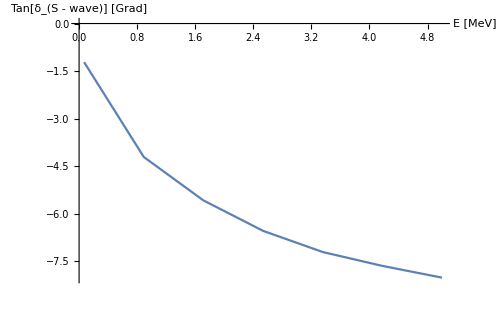
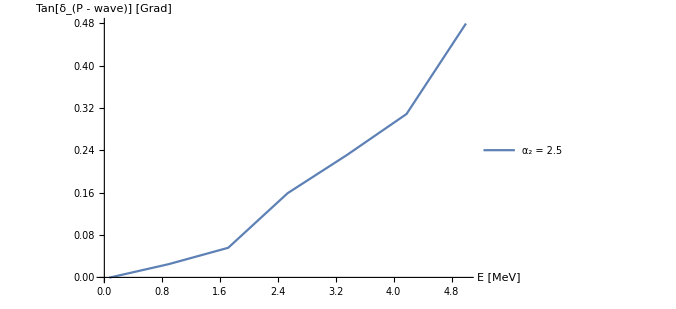
-Graphics- | -Graphics-

```mathematica
tanDsL=Get[LocalObject["tanDsL"]];tanDpL=Get[LocalObject["tanDpL"]];αL=Get[LocalObject["3-1_CorePara_P"]];
cselect=c2Range[[1]];
pLength=Length[a2Range];
Print["Plotting  ϕ_core += c_2×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with c_2=",NumberForm[cselect,nf]];
phaseS=Table[Transpose[{Select[tanDsL,#[[1]]==cselect&][[All,3]][[1]][[All,1]],(180./Pi) ArcTan[Select[tanDsL,#[[1]]==cselect&][[All,3]][[nn]][[All,2]]]}],{nn,pLength}];
phaseP=Table[Transpose[{Select[tanDpL,#[[1]]==cselect&][[All,3]][[1]][[All,1]],(180./Pi) ArcTan[Select[tanDpL,#[[1]]==cselect&][[All,3]][[nn]][[All,2]]]}],{nn,pLength}];
leg="α_2 = "<>ToString[#]&/@a2Range;
Grid[{{ListPlot[phaseS,AxesLabel->{"E [MeV]","Tan[δ_(S - wave)] [Grad]"},ImageSize->500,PlotRange->{Automatic,Automatic},Joined->True],
ListPlot[phaseP,AxesLabel->{"E [MeV]","Tan[δ_(P - wave)] [Grad]"},ImageSize->500,PlotRange->{Automatic,Automatic},Joined->True,PlotLegends->leg]}}]
```

Plotting  ϕ_core += c_2×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=2.5000

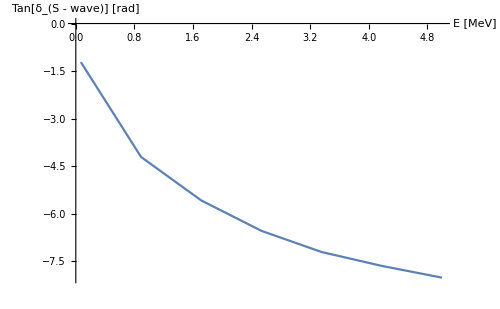
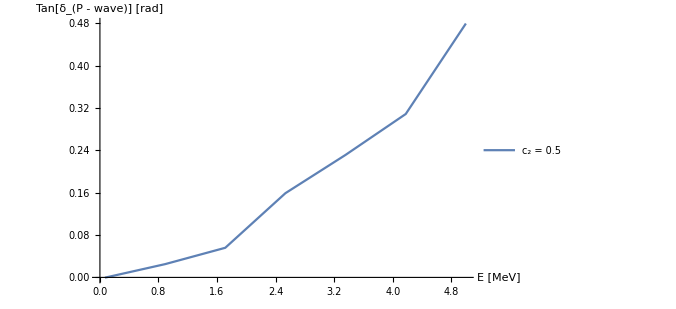
-Graphics- | -Graphics-

```mathematica
aselect=a2Range[[1]];
pLength=Length[c2Range];
Print["Plotting  ϕ_core += c_2×e^(-SubscriptBox[α, 2] SuperscriptBox[ρ, 2]) with α_2=",NumberForm[aselect,nf]];
phaseS=Table[Transpose[{Select[tanDsL,#[[2]]==aselect&][[All,3]][[1]][[All,1]],(180./Pi) ArcTan[Select[tanDsL,#[[2]]==aselect&][[All,3]][[nn]][[All,2]]]}],{nn,pLength}];
phaseP=Table[Transpose[{Select[tanDpL,#[[2]]==aselect&][[All,3]][[1]][[All,1]],(180./Pi) ArcTan[Select[tanDpL,#[[2]]==aselect&][[All,3]][[nn]][[All,2]]]}],{nn,pLength}];
leg="c_2 = "<>ToString[#]&/@c2Range;
Grid[{{ListPlot[phaseS,AxesLabel->{"E [MeV]","Tan[δ_(S - wave)] [rad]"},ImageSize->500,PlotRange->{Automatic,Automatic},Joined->True],
ListPlot[phaseP,AxesLabel->{"E [MeV]","Tan[δ_(P - wave)] [rad]"},ImageSize->500,PlotRange->{Automatic,Automatic},Joined->True,PlotLegends->leg]}}]
```

λ = 16.  c_2 = 0.5000  α_2 = 2.5000:  a_s = 0.427987 fm    r_s = -6.78622 fm        a_p = 0.288589 fm^3     r_p = 330.226 fm

/home/kirscher/kette_repo/AcoreNteraction/source_mathematica/../data/TwoGaussCore_EREpara.dat

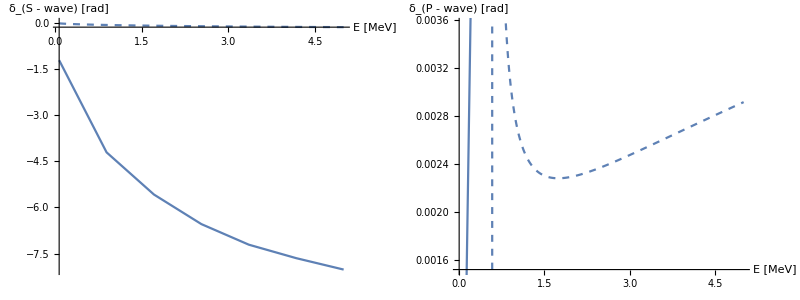

```mathematica
f1=1;f2=5;
exportTab={};
dataTab={};
α1=Select[αL,#[[1]]==λ&][[1]][[2]];
Do[
Lrel = 0;
dataS=Transpose[{(Sqrt[2 μ ErangeMeV]/hbar),(Sqrt[2 μ ErangeMeV]/hbar)/Select[tanDsL,#[[2]]==aselect&&#[[1]]==cselect&][[1]][[3]][[All,2]]}];
EreS=Fit[dataS[[f1;;f2]],{1,p^2},p];
a0tf=-Coefficient[EreS,p,0]^-1;
r0tf= Coefficient[EreS,p,2]*2.;
Lrel = 1;
dataP=Transpose[{(Sqrt[2 μ ErangeMeV]/hbar),(Sqrt[2 μ ErangeMeV]/hbar)^3/Select[tanDpL,#[[2]]==aselect&&#[[1]]==cselect&][[1]][[3]][[All,2]]}];
EreP=Fit[dataP[[f1;;f2]],{1,p^2},p];
a1tf=-Coefficient[EreP,p,0]^-1;
r1tf= Coefficient[EreP,p,2]*2.;

AppendTo[exportTab,{NumberForm[λ,nf],NumberForm[1.0,nf],NumberForm[α1,nf],NumberForm[cselect,nf],NumberForm[α1 aselect,nf],NumberForm[a0tf,nf],NumberForm[r0tf,nf],NumberForm[a1tf,nf],NumberForm[r1tf,nf]}];
AppendTo[dataTab,{λ,1.0,α1,cselect,α1 aselect,a0tf,r0tf,a1tf,r1tf}];

λ=0.25 activeLEC⟦nn⟧[[1]]^2;
Print["λ = ",λ,"  c_2 = ",NumberForm[cselect,nf],"  α_2 = ",NumberForm[aselect,nf],":  a_s = ",a0tf," fm    r_s = ",r0tf," fm        a_p = ",a1tf," fm^3     r_p = ",r1tf," fm"];
,{aselect,a2Range},{cselect,c2Range}]
Export[NotebookDirectory[]<>"../data/TwoGaussCore_EREpara.dat",exportTab,"Table"]
Grid[{{
Show[Plot[(Sqrt[2 μ ee]/hbar)/(-1./#[[6]]+(#[[7]])/2 (Sqrt[2 μ ee]/hbar)^2)&/@dataTab,{ee,phaseS[[1]][[All,1]][[1]],phaseS[[1]][[All,1]][[-1]]},PlotStyle->Dashed,AxesLabel->{"E [MeV]","δ_(S - wave) [rad]"},ImageSize->500],
ListPlot[phaseS,Joined->True],PlotRange->{Automatic,Automatic}],
Show[Plot[(Sqrt[2 μ ee]/hbar)^3/(-1./#[[8]]+(#[[9]])/2 (Sqrt[2 μ ee]/hbar)^2)&/@dataTab,{ee,phaseP[[1]][[All,1]][[1]],phaseP[[1]][[All,1]][[-1]]},PlotStyle->Dashed,AxesLabel->{"E [MeV]","δ_(P - wave) [rad]"},ImageSize->500,PlotRange->{Automatic,Automatic}],
ListPlot[phaseP,Joined->True]]
}}]
```